```mathematica
nf12=f12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1};
nf22=f22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1};
nf32=f32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1};
nf3t2=Together[nf32];
nf3s2=Cancel[Simplify[(Numerator[nf3t2]-Coefficient[Numerator[nf3t2],k1,0])]/Denominator[nf3t2]]/.{k1->0};
nf1=f12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1};
nf2=f22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1};
nf3=f32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1};
nf3t=Together[nf3];
nf3s=Cancel[Simplify[(Numerator[nf3t]-Coefficient[Numerator[nf3t],k1,0])]/Denominator[nf3t]]/.{k1->0};
```

```mathematica
unf12=uf12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1};
unf22=uf22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1};
unf32=uf32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1};
unf3t2=Together[unf32];
unf3s2=Cancel[Simplify[(Numerator[unf3t2]-Coefficient[Numerator[unf3t2],k1,0])]/Denominator[unf3t2]]/.{k1->0};
unf1=uf12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1};
unf2=uf22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1};
unf3=uf32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1};
unf3t=Together[unf3];
unf3s=Cancel[Simplify[(Numerator[unf3t]-Coefficient[Numerator[unf3t],k1,0])]/Denominator[unf3t]]/.{k1->0};
```

```mathematica
nf13=f12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.3,Λ->L1,P1->1,Q->1};
nf23=f22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.3,Λ->L1,P1->1,Q->1};
nf33=f32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.3,Λ->L1,P1->1,Q->1};
nf3t3=Together[nf33];
nf3s3=Cancel[Simplify[(Numerator[nf3t3]-Coefficient[Numerator[nf3t3],k1,0])]/Denominator[nf3t3]]/.{k1->0};
unf13=uf12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.3,Λ->L1,P1->1,Q->1};
unf23=uf22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.3,Λ->L1,P1->1,Q->1};
unf33=uf32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.3,Λ->L1,P1->1,Q->1};
unf3t3=Together[unf33];
unf3s3=Cancel[Simplify[(Numerator[unf3t3]-Coefficient[Numerator[unf3t3],k1,0])]/Denominator[unf3t3]]/.{k1->0};
```

```mathematica
tf=f12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,Q->1};
```

```mathematica
Simplify[tf/.{y->-0.1,k3->2,θ->π/3}]
```

0.+0.0091944 ⅈ

```mathematica
f4=Query[4,1]@a;
f5=Query[5,1]@a;
f42=f4/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
f52=f5/.{q3->(-(2ξ)^2 MB^2+(1-ξ^2)Q^2)^(1/2)};
```

```mathematica
nf4=f42/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1};
nf5=f52/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1};
```

```mathematica
NIntegrate[nf1,{y,-0.1*2,0},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf2,{y,0,1-0.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf3s,{x,0,1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

3.538282839 ⅈ

```mathematica
NIntegrate[nf12,{y,-0.2*2,0},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf22,{y,0,1-0.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf3s2,{x,0,1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

2.09905779 ⅈ

```mathematica
NIntegrate[nf4,{y,-0.1*2,0},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf5,{y,0,1-0.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

1.394152267 ⅈ

```mathematica
NIntegrate[nf1,{y,-0.1*2,0},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf2,{y,0,1-0.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

1.394152267 ⅈ

```mathematica
nf3s
```

1/((1.+k3^2-0.980928 x)^4)771.605 k3 ((0.+0.00391752 ⅈ)+(0.+0.00387872 ⅈ) k3^2-(0.+0.0160536 ⅈ) x-(0.+0.0116362 ⅈ) k3^2 x+(0.+0.0246556 ⅈ) x^2+(0.+0.0116362 ⅈ) k3^2 x^2-(0.+0.0168206 ⅈ) x^3-(0.+0.00387872 ⅈ) k3^2 x^3+(0.+0.00430102 ⅈ) x^4-(1.0842×10^-18+0.00409117 ⅈ) k3 Cos[θ]+(3.25261×10^-18+0.0122735 ⅈ) k3 x Cos[θ]-(3.25261×10^-18+0.0122735 ⅈ) k3 x^2 Cos[θ]+(1.0842×10^-18+0.00409117 ⅈ) k3 x^3 Cos[θ])

```mathematica
unf3s
```

1/((1.+k3^2-0.980928 x)^4)516.529 k3 ((0.-0.0115142 ⅈ)-(0.+0.00623968 ⅈ) k3^2+(0.+0.040167 ⅈ) x+(0.+0.018719 ⅈ) k3^2 x-(0.+0.0514158 ⅈ) x^2-(0.+0.018719 ⅈ) k3^2 x^2+(0.+0.0283874 ⅈ) x^3+(0.+0.00623968 ⅈ) k3^2 x^3-(0.+0.0056244 ⅈ) x^4-(1.30104×10^-18+0.00609884 ⅈ) k3 Cos[θ]+(3.90313×10^-18+0.0182965 ⅈ) k3 x Cos[θ]-(3.90313×10^-18+0.0182965 ⅈ) k3 x^2 Cos[θ]+(1.30104×10^-18+0.00609884 ⅈ) k3 x^3 Cos[θ])

```mathematica
NIntegrate[unf12,{y,0,0.2*2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[unf22,{y,0.2*2,1+0.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[unf3s2,{x,0,1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-1.8469319 ⅈ

```mathematica
NIntegrate[unf1,{y,0,0.1*2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[unf2,{y,0.1*2,1+0.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[unf3s,{x,0,1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-3.28616093 ⅈ

```mathematica
3.5382828386462027234`10.-3.2861609321959957891`9.687092700851611
```

0.25212191

```mathematica
2.0990577939494301643`9.952302099060816-1.84693189580338856326316432365786113223`9.687411541123975
```

0.2521259

```mathematica
NIntegrate[nf13,{y,-0.3*2,0},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf23,{y,0,1-0.3},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf3s3,{x,0,1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[unf13,{y,0,0.3*2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[unf23,{y,0.3*2,1+0.3},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[unf3s3,{x,0,1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

0.25228278 ⅈ

```mathematica
(*上面是我的下面是分开的delta*)
```

```mathematica
nf12=f12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1};
nf22=f22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1};
nf32=f32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1,k1->0};
nf1=f12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1};
nf2=f22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1};
nf3=f32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1,k1->0};unf12=uf12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1};
unf22=uf22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1};
unf32=uf32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1,k1->0};
unf1=uf12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1};
unf2=uf22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1};
unf3=uf32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1,k1->0};
```

```mathematica
NIntegrate[nf12,{y,-0.2*2,0},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf22,{y,0,1-0.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf32,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[unf12,{y,0,0.2*2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[unf22,{y,0.2*2,1+0.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[unf32,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-0.38833849 ⅈ

```mathematica
NIntegrate[nf1,{y,-0.1*2,0},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf2,{y,0,1-0.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf3,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[unf1,{y,0,0.1*2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[unf2,{y,0.1*2,1+0.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[unf3,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]
```

-1.74995178 ⅈ

```mathematica
NIntegrate[nf12,{y,-0.2*2,0},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf22,{y,0,1-0.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf32,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]-(NIntegrate[unf12,{y,0,0.2*2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[unf22,{y,0.2*2,1+0.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[unf32,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10])
```

-3.72889011 ⅈ

```mathematica
NIntegrate[nf1,{y,-0.1*2,0},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf2,{y,0,1-0.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf3,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]-(NIntegrate[unf1,{y,0,0.1*2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[unf2,{y,0.1*2,1+0.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[unf3,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10])
```

-3.60009646 ⅈ

```mathematica
(*he2 part*)
```

```mathematica
nf12=f12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1};
nf22=f22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1};
nf32=f32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1,k1->0};
nf1=f12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1};
nf2=f22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1};
nf3=f32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1,k1->0};unf12=uf12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1};
unf22=uf22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1};
unf32=uf32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1,k1->0};
unf1=uf12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1};
unf2=uf22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1};
unf3=uf32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1,k1->0};
```

```mathematica
nf13=f12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.3,Λ->L1,P1->1,Q->1};
nf23=f22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.3,Λ->L1,P1->1,Q->1};
nf33=f32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.3,Λ->L1,P1->1,Q->1,k1->0};
nf14=f12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.4,Λ->L1,P1->1,Q->1};
nf24=f22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.4,Λ->L1,P1->1,Q->1};
nf34=f32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.4,Λ->L1,P1->1,Q->1,k1->0};unf13=uf12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.3,Λ->L1,P1->1,Q->1};
unf23=uf22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.3,Λ->L1,P1->1,Q->1};
unf33=uf32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.3,Λ->L1,P1->1,Q->1,k1->0};
unf14=uf12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.4,Λ->L1,P1->1,Q->1};
unf24=uf22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.4,Λ->L1,P1->1,Q->1};
unf34=uf32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.4,Λ->L1,P1->1,Q->1,k1->0};
```

```mathematica
NIntegrate[nf1,{y,-0.1*2,0},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf2,{y,0,1-0.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf3,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]-(NIntegrate[unf1,{y,0,0.1*2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[unf2,{y,0.1*2,1+0.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[unf3,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10])
```

-0.39477473 ⅈ

```mathematica
NIntegrate[nf12,{y,-0.2*2,0},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf22,{y,0,1-0.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf32,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]-(NIntegrate[unf12,{y,0,0.2*2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[unf22,{y,0.2*2,1+0.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[unf32,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10])
```

-0.39476398 ⅈ

```mathematica
NIntegrate[nf13,{y,-0.3*2,0},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf23,{y,0,1-0.3},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf33,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]-(NIntegrate[unf13,{y,0,0.3*2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[unf23,{y,0.3*2,1+0.3},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[unf33,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10])
```

-0.3946004 ⅈ

```mathematica
NIntegrate[nf14,{y,-0.4*2,0},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf24,{y,0,1-0.4},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[nf34,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]-(NIntegrate[unf14,{y,0,0.4*2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[unf24,{y,0.4*2,1+0.4},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[unf34,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10])
```

-0.39472427 ⅈ

```mathematica
ng12=g12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1};
ng22=g22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1};
ng32=g32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1,k1->0};
ng1=g12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1};
ng2=g22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1};
ng3=g32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1,k1->0};ung12=ug12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1};
ung22=ug22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1};
ung32=ug32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1,k1->0};
ung1=ug12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1};
ung2=ug22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1};
ung3=ug32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1,k1->0};
```

```mathematica
ng13=g12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.3,Λ->L1,P1->1,Q->1};
ng23=g22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.3,Λ->L1,P1->1,Q->1};
ng33=g32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.3,Λ->L1,P1->1,Q->1,k1->0};
ng14=g12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.4,Λ->L1,P1->1,Q->1};
ng24=g22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.4,Λ->L1,P1->1,Q->1};
ng34=g32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.4,Λ->L1,P1->1,Q->1,k1->0};ung13=ug12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.3,Λ->L1,P1->1,Q->1};
ung23=ug22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.3,Λ->L1,P1->1,Q->1};
ung33=ug32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.3,Λ->L1,P1->1,Q->1,k1->0};
ung14=ug12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.4,Λ->L1,P1->1,Q->1};
ung24=ug22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.4,Λ->L1,P1->1,Q->1};
ung34=ug32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.4,Λ->L1,P1->1,Q->1,k1->0};
```

```mathematica
NIntegrate[ng1,{y,-0.1*2,0},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[ng2,{y,0,1-0.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[ng3,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]-(NIntegrate[ung1,{y,0,0.1*2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[ung2,{y,0.1*2,1+0.1},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[ung3,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10])
```

-5.06447559 ⅈ

```mathematica
NIntegrate[ng12,{y,-0.2*2,0},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[ng22,{y,0,1-0.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[ng32,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]-(NIntegrate[ung12,{y,0,0.2*2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[ung22,{y,0.2*2,1+0.2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[ung32,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10])
```

-5.06428267 ⅈ

```mathematica
NIntegrate[ng13,{y,-0.3*2,0},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[ng23,{y,0,1-0.3},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[ng33,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]-(NIntegrate[ung13,{y,0,0.3*2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[ung23,{y,0.3*2,1+0.3},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[ung33,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10])
```

-5.06430075 ⅈ

```mathematica
NIntegrate[ng14,{y,-0.4*2,0},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[ng24,{y,0,1-0.4},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[ng34,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]-(NIntegrate[ung14,{y,0,0.4*2},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[ung24,{y,0.4*2,1+0.4},{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10]+NIntegrate[ung34,{x,0,1},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10])
```

-5.06438199 ⅈ

```mathematica
(-2*0.76)^2/(2(0.093)^2)
```

133.565

```mathematica
0.3947242700701553978`8.715365742307695 *133.5645739391837/(2*(2π)^4)
```

0.0169136

```mathematica
5.0643007502789627738`9.436157511557687 *133.5645739391837/(2*(2π)^4)
```

0.217001

```mathematica
0.016913583987560096/4
```

0.0042284

```mathematica
0.0042288925441174505
```

```mathematica
-0.7321741215916416 cc["C"]^2 ((3.1010659278175945+12.210503913246692 Q2+9.401132818445708 Q2^2-6.133088308620712 Q2^3-0.9422147793584509 Q2^4)/((1.+Q2)^2 (3.5268839999999995+Q2)^2 (0.5589646935628828+1.3319130214098929 Q2+1. Q2^2))+(-1.6365189604842696-5.0175826253187195 Q2-4.3213561053199685 Q2^2+1.1039865260179034 Q2^3+0.18771607459763834 Q2^4)/((1.+Q2)^2 (3.5268839999999995+Q2)^2 (0.5589646935628828+1.3319130214098929 Q2+1. Q2^2))+(-9.83691395391789+14.595209772303287 Q2+46.162993690959205 Q2^2+28.982808195291803 Q2^3+6.735860429718742 Q2^4+0.4936465238065286 Q2^5-0.008976011327180676 Q2^6)/(Q2 (1.+Q2)^2 (3.5268839999999995+Q2) (4.+Q2) (2.236400909058625+1. Q2)^2)+(-1.5828877185253056-10.35952601659917 Q2-17.240590519379655 Q2^2-4.160293641856567 Q2^3+7.94657872676447 Q2^4+5.854996869209542 Q2^5+1.4053480333716264 Q2^6+0.1034707654985628 Q2^7)/((1.+Q2)^2 (3.5268839999999995+Q2)^2 (2.236400909058625+1. Q2)^3 (0.5589646935628828+1.3319130214098929 Q2+1. Q2^2))+(-63.05156382726796-259.38309154272645 Q2-440.24477413457714 Q2^2-355.7441429338316 Q2^3-124.79771133585422 Q2^4-10.816837916500722 Q2^5+2.516807888868121 Q2^6+0.29020356995900687 Q2^7)/((2.236400909058625+1. Q2)^3 (3.5268839999999995+4.526883999999999 Q2+Q2^2)^2 (0.5589646935628828+1.3319130214098929 Q2+1. Q2^2))+(-1.8824729325175074-0.12188400069693711 Q2+9.299417481569407 Q2^2-1.9489436641028544 Q2^3-27.410547015083235 Q2^4-19.23788284301528 Q2^5-3.4165189714186894 Q2^6-0.17087708078133235 Q2^7+0.018116004104184034 Q2^8)/(Q2^2 (1.+Q2)^2 (3.5268839999999995+Q2)^2 (0.5589646935628828+1.3319130214098929 Q2+1. Q2^2))-(0.0091505266018253 (79233.82285220492+75064.51612933248 Q2-88123.41656671441 Q2^2-157855.239652459 Q2^3-92245.63233690306 Q2^4-26969.392129430784 Q2^5-4126.221322001425 Q2^6-278.4595904320773 Q2^7+1.9449071671758766 Q2^8+1. Q2^9) DiscBChop[-Q2,1.,1.])/((2.236400909058625+1. Q2)^3 (14.107535999999998+21.63442 Q2+8.526883999999999 Q2^2+Q2^3)^2)+(0.009150526601825302 (-101.93037781916253-114.5524151378507 Q2+506.3417628217091 Q2^2+569.0202378333228 Q2^3-1395.1546023155506 Q2^4-2723.8709594239635 Q2^5-1476.1239039145355 Q2^6-226.34221659481074 Q2^7-8.413310928590116 Q2^8+1. Q2^9) DiscBChop[-Q2,0.1381,1.])/(Q2 (1.+Q2)^2 (3.5268839999999995+Q2)^2 (0.5589646935628828+1.3319130214098929 Q2+1. Q2^2) Kallenλ[0.01907161,1.,-Q2])+(0.3979359999999998 (-5.395430719717959-16.23087612492213 Q2+5.8565367265787 Q2^2+1. Q2^3) ScalarC0Chop[0.8817209999999999,0.8817209999999999,-Q2,1.,1.232,0.1381])/((1.+Q2)^2 (3.5268839999999995+Q2)^2)-(0.3979359999999998 (-6.071226941281689-16.23087612492213 Q2+5.8565367265787 Q2^2+1. Q2^3) ScalarC0Chop[0.8817209999999999,0.8817209999999999,-Q2,1.,1.232,1.])/((1.+Q2)^2 (3.5268839999999995+Q2)^2))/.{Q2->1, cc["C"]->(-2*0.76)}
```

0.00422889

```mathematica
-1/Q2^2 0.7321741215916416 cc["C"]^2 (-((0.6622533412993622 Q2 (-2.958460202516318-8.150960821749976 Q2-7.566832575988182 Q2^2+1.1837294393015227 Q2^3+6.268846407824584 Q2^4+1. Q2^5))/((1.+Q2)^2 (3.5268839999999995+Q2)^2 (0.5589646935628828+1.3319130214098929 Q2+1. Q2^2)))+(2.9369391913135936 Q2 (-1.2641100757748327-1.5931162851496212 Q2+1.620502432835477 Q2^2+6.711043754395948 Q2^3+6.825497668077887 Q2^4+1. Q2^5))/((1.+Q2)^2 (3.5268839999999995+Q2)^2 (0.5589646935628828+1.3319130214098929 Q2+1. Q2^2))-(1.0070956809921174 Q2 (-31.688902040252252+8.918165137417013 Q2+67.2672704759619 Q2^2+45.83205950811737 Q2^3+11.50276436560853 Q2^4+1. Q2^5))/((1.+Q2)^2 (3.5268839999999995+Q2) (4.+Q2) (2.236400909058625+1. Q2)^2)+(-6.917004410812402-33.93137455465281 Q2-62.09811837962489 Q2^2-34.26534426746417 Q2^3+20.848632107419213 Q2^4+24.181669106175644 Q2^5+5.834377963447799 Q2^6+0.5269985449116166 Q2^7)/((1.+Q2)^2 (3.5268839999999995+Q2)^2 (0.5589646935628828+1.3319130214098929 Q2+1. Q2^2))-(1.480176852248612 Q2 (-20.22748338463441-116.43922549854318 Q2-260.04698308594976 Q2^2-279.66425696012004 Q2^3-117.2760804845521 Q2^4+28.82755686803172 Q2^5+40.60728230876435 Q2^6+11.596048910428607 Q2^7+1. Q2^8))/((1.+Q2)^2 (3.5268839999999995+Q2)^2 (2.236400909058625+1. Q2)^3 (0.5589646935628828+1.3319130214098929 Q2+1. Q2^2))-(0.2981908322546326 Q2 (-11.70843377269459-20.39922777944802 Q2+29.484485711687146 Q2^2+146.88791679592995 Q2^3+228.76640874033677 Q2^4+176.0460539134183 Q2^5+70.32205150478876 Q2^6+13.710546626593958 Q2^7+1. Q2^8))/((1.+Q2)^2 (3.5268839999999995+Q2)^2 (2.236400909058625+1. Q2)^3 (0.5589646935628828+1.3319130214098929 Q2+1. Q2^2))-(0.26619083196295035 Q2 (-4033.3111187704967-12035.013005418277 Q2-9449.982606369442 Q2^2+3002.3302760648144 Q2^3+8351.964206235474 Q2^4+5159.872199182896 Q2^5+1598.5826472407405 Q2^6+274.41502492943624 Q2^7+25.25690571964844 Q2^8+1. Q2^9) DiscBChop[-Q2,1.,1.])/((2.236400909058625+1. Q2)^3 (14.107535999999998+21.63442 Q2+8.526883999999999 Q2^2+Q2^3)^2)+(0.26619083196295046 Q2 (-12.874961545594099-76.79379736065496 Q2-172.36889831854586 Q2^2-149.5988144478896 Q2^3+29.892812471523346 Q2^4+138.0810718456733 Q2^5+80.4663772465772 Q2^6+14.898687623882456 Q2^7+1. Q2^8) DiscBChop[-Q2,0.1381,1.])/((1.+Q2)^2 (3.5268839999999995+Q2)^2 (0.5589646935628828+1.3319130214098929 Q2+1. Q2^2) Kallenλ[0.01907161,1.,-Q2])-(1.1568479999999997 Q2 (-3.6774815527287354-6.237000966839766 Q2-1.6482019833209043 Q2^2+5.712325179402999 Q2^3+1. Q2^4) ScalarC0Chop[0.8817209999999999,0.8817209999999999,-Q2,1.,1.232,0.1381])/((1.+Q2)^2 (3.5268839999999995+Q2)^2)+(1.1568479999999997 Q2 (-3.404192263913251-6.391975890208653 Q2-1.6482019833209043 Q2^2+5.712325179402999 Q2^3+1. Q2^4) ScalarC0Chop[0.8817209999999999,0.8817209999999999,-Q2,1.,1.232,1.])/((1.+Q2)^2 (3.5268839999999995+Q2)^2))/.{Q2->1, cc["C"]->(-2*0.76)}
```

0.0542493

```mathematica
0.21700078402294104/4
```

0.0542502

```mathematica
nf12[y_]=Together[f12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1}];
nf22[y_]=Together[f22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1}];
nf32=f32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1,k1->0};
nf1[y_]=Together[f12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1}];
nf2[y_]=Together[f22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1}];
nf3=f32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1,k1->0};unf12[y_]=Together[uf12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1}];
unf22[y_]=Together[uf22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1}];
unf32=uf32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1,k1->0};
unf1[y_]=Together[uf12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1}];
unf2[y_]=Together[uf22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1}];
unf3=uf32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1,k1->0};
ng12[y_]=Together[g12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1}];
ng22[y_]=Together[g22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1}];
ng32=g32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1,k1->0};
ng1[y_]=Together[g12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1}];
ng2[y_]=Together[g22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1}];
ng3=g32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1,k1->0};ung12[y_]=Together[ug12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1}];
ung22[y_]=Together[ug22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1}];
ung32=ug32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.2,Λ->L1,P1->1,Q->1,k1->0};
ung1[y_]=Together[ug12/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1}];
ung2[y_]=Together[ug22/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1}];
ung3=ug32/.{MB->0.939,mm->0.1381,MM->0.939,MT->1.232,ξ->0.1,Λ->L1,P1->1,Q->1,k1->0};
```

```mathematica
tinf1[y_]:=NIntegrate[nf1[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
tinf2[y_]:=NIntegrate[nf2[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
ting1[y_]:=NIntegrate[ng1[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
ting2[y_]:=NIntegrate[ng2[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
uinf1[y_]:=NIntegrate[unf1[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
uinf2[y_]:=NIntegrate[unf2[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
uing1[y_]:=NIntegrate[ung1[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
uing2[y_]:=NIntegrate[ung2[y],{k3,0,∞},{θ,0,2π},WorkingPrecision->10,MaxRecursion->20,MinRecursion ->10];
```

```mathematica
tlf1=ParallelTable[{y,tinf1[y]},{y,-0.1*2,0,0.01}];
tlf2=ParallelTable[{y,tinf2[y]},{y,0,1-0.1,0.01}];
tlg1=ParallelTable[{y,ting1[y]},{y,-0.1*2,0,0.01}];
tlg2=ParallelTable[{y,ting2[y]},{y,0,1-0.1,0.01}];
ulf1=ParallelTable[{y,uinf1[y]},{y,0,0.1*2,0.01}];
ulf2=ParallelTable[{y,uinf2[y]},{y,0.1*2,1+0.1,0.01}];
ulg1=ParallelTable[{y,uing1[y]},{y,0,0.1*2,0.01}];
ulg2=ParallelTable[{y,uing2[y]},{y,0.1*2,1+0.1,0.01}];
```

```mathematica
tf1=Interpolation[tlf1];
tf2=Interpolation[tlf2];
tg1=Interpolation[tlg1];
tg2=Interpolation[tlg2];
uf1=Interpolation[ulf1];
uf2=Interpolation[ulf2];
ug1=Interpolation[ulg1];
ug2=Interpolation[ulg2];
```

```mathematica
pathtf01=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"t-f-0.1.pdf"}];
Export[pathtf01,Labeled[Show[Plot[(-I)*tf1[x],{x,-0.2,0},PlotRange->{{-0.2,1},All},PlotStyle->{Black,Thick}],Plot[(-I)*tf2[x],{x,0,0.9},PlotRange->{{-0.2,1},All},PlotStyle->{Black,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[f,t],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Top,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\t-f-0.1.pdf

```mathematica
pathtg01=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"t-g-0.1.pdf"}];
Export[pathtg01,Labeled[Show[Plot[(-I)*tg1[x],{x,-0.2,0},PlotRange->{{-0.2,1},All},PlotStyle->{Black,Thick}],Plot[(-I)*tg2[x],{x,0,0.9},PlotRange->{{-0.2,1},All},PlotStyle->{Black,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[g,t],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Top,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\t-g-0.1.pdf

```mathematica
SystemOpen["G:\\output\\summary\\gpd\\pic\\t-g-0.1.pdf"]
```

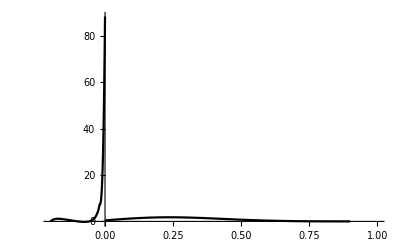
-Graphics-f_tyξ=0.1

```mathematica
Labeled[Show[Plot[(-I)*tf1[x],{x,-0.2,0},PlotRange->{{-0.2,1},All},PlotStyle->{Black,Thick}],Plot[(-I)*tf2[x],{x,0,0.9},PlotRange->{{-0.2,1},All},PlotStyle->{Black,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[f,t],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Top,Right},LabelStyle->24]
```

```mathematica
pathuf01=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"u-f-0.1.pdf"}];
Export[pathuf01,Labeled[Show[Plot[(-I)*uf1[x],{x,0,0.2},PlotRange->{{0,1.1},All},PlotStyle->{Black,Thick}],Plot[(-I)*uf2[x],{x,0.2,1.1},PlotRange->{{0,1.1},All},PlotStyle->{Black,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[f,u],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Top,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\u-f-0.1.pdf

```mathematica
pathug01=FileNameJoin[{"G:\\output\\summary\\gpd\\pic",
"u-g-0.1.pdf"}];
Export[pathug01,Labeled[Show[Plot[(-I)*ug1[x],{x,0,0.2},PlotRange->{{0,1.1},All},PlotStyle->{Black,Thick}],Plot[(-I)*ug2[x],{x,0.2,1.1},PlotRange->{{0,1.1},All},PlotStyle->{Black,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[g,u],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Top,Right},LabelStyle->24]]
```

G:\output\summary\gpd\pic\u-g-0.1.pdf

```mathematica
SystemOpen["G:\\output\\summary\\gpd\\pic\\u-g-0.1.pdf"]
```

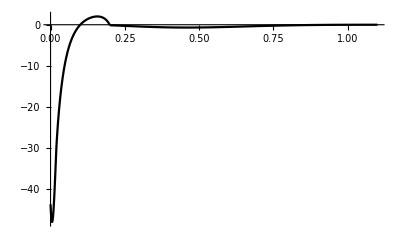
-Graphics-f_uyξ=0.1

```mathematica
Labeled[Show[Plot[(-I)*uf1[x],{x,0,0.2},PlotRange->{{0,1.1},All},PlotStyle->{Black,Thick}],Plot[(-I)*uf2[x],{x,0.2,1.1},PlotRange->{{0,1.1},All},PlotStyle->{Black,Thick}],AxesStyle->Directive[16]],
{StyleBox[SubscriptBox[f,u],FontSlant->"Italic"]//DisplayForm,
ToString[TraditionalForm[y]],"ξ=0.1"},{Left,Top,Right},LabelStyle->24]
```